# 曲面相交

```mathematica
ContourPlot3D[{x^2+y^2+z^2==1,z==x^2+y^2},{x,-1,1},{y,-1,1},{z,-1,1},Mesh->None,ContourStyle->Opacity[0.8]]
```

-Graphics3D-

```mathematica
Solve[{x^2+y^2+z^2==1,z==x^2+y^2},{x,y},Reals]
```

{}

```mathematica
Solve[{x^2+y^2+z^2==1,z==x^2+y^2},{x,y,z},Reals]
```

Solve::svars: 方程可能无法给出所有 " solve " 变量的解.

{{y→ConditionalExpression[-√((√5)/2+1/2 (-1-2 x^2)), ],z→ConditionalExpression[(√5)/2+x^2+1/2 (-1-2 x^2), ]},{y→ConditionalExpression[√((√5)/2+1/2 (-1-2 x^2)), ],z→ConditionalExpression[(√5)/2+x^2+1/2 (-1-2 x^2), ]}}

```mathematica
Solve[{x^2+y^2+z^2==1,z==x^2+y^2},{y,z},Reals]
```

{{y→ConditionalExpression[-√((√5)/2+1/2 (-1-2 x^2)), ],z→ConditionalExpression[(√5)/2+x^2+1/2 (-1-2 x^2), ]},{y→ConditionalExpression[√((√5)/2+1/2 (-1-2 x^2)), ],z→ConditionalExpression[(√5)/2+x^2+1/2 (-1-2 x^2), ]}}

```mathematica
curve={x,y,z}/.%
```

{{x,ConditionalExpression[-√((√5)/2+1/2 (-1-2 x^2)), ],ConditionalExpression[(√5)/2+x^2+1/2 (-1-2 x^2), ]},{x,ConditionalExpression[√((√5)/2+1/2 (-1-2 x^2)), ],ConditionalExpression[(√5)/2+x^2+1/2 (-1-2 x^2), ]}}

```mathematica
ParametricPlot3D[curve,{x,-1,1}]
```

-Graphics3D-

如果直接化简两个方程

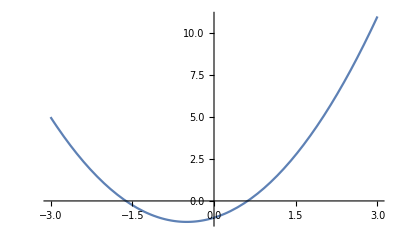

```mathematica
Plot[z^2+z-1,{z,-3,3}]
```

```mathematica
Reduce[{x^2+y^2+z^2==1,z==x^2+y^2},{y,z},Reals]
```

-√(1/2 (-1+√5))≤x≤√(1/2 (-1+√5))&&(y==-√((√5)/2+1/2 (-1-2 x^2))||y==√((√5)/2+1/2 (-1-2 x^2)))&&z==x^2+y^2